# Изпит-Георги Г.-2001261019

## Генериране на данни

```mathematica
xt = Table[1+i*0.5, {i, -5, 5}]
```

{-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5}

```mathematica
f[x_]:=x-10Cos[x]
```

```mathematica
yt=f[xt]
```

{-2.20737,-6.40302,-9.27583,-10.,-8.27583,-4.40302,0.792628,6.16147,10.5114,12.8999,12.8646}

```mathematica
xt^2
```

{2.25,1.,0.25,0.,0.25,1.,2.25,4.,6.25,9.,12.25}

```mathematica
yt*xt
```

{3.31106,6.40302,4.63791,0.,-4.13791,-4.40302,1.18894,12.3229,26.2786,38.6998,45.026}

```mathematica
xt^3
```

{-3.375,-1.,-0.125,0.,0.125,1.,3.375,8.,15.625,27.,42.875}

```mathematica
xt^4
```

{5.0625,1.,0.0625,0.,0.0625,1.,5.0625,16.,39.0625,81.,150.063}

```mathematica
yt*xt^2
```

{-4.96659,-6.40302,-2.31896,0.,-2.06896,-4.40302,1.78341,24.6459,65.6965,116.099,157.591}

```mathematica
P=Length[xt]
```

11

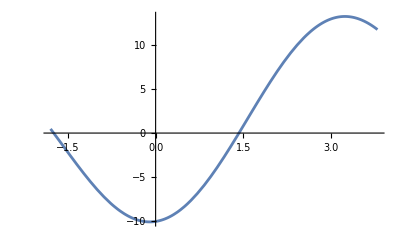

```mathematica
grf = Plot[f[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}]
```

```mathematica
points = Table[{xt[[i]], yt[[i]]}, {i, 1, P}];
```

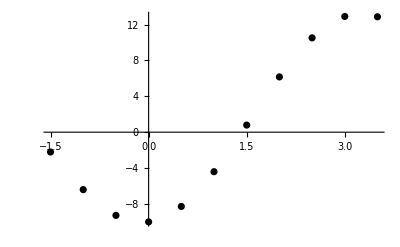

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

## Линейна регресия

### Попълваме таблицата

```mathematica
xt^2
```

{2.25,1.,0.25,0.,0.25,1.,2.25,4.,6.25,9.,12.25}

```mathematica
yt*xt
```

{3.31106,6.40302,4.63791,0.,-4.13791,-4.40302,1.18894,12.3229,26.2786,38.6998,45.026}

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]]}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]};
```

```mathematica
LinearSolve[A,b]
```

{0.49398,0.0365801}

### Съставяме полинома

```mathematica
P1[x_] := 0.49398 + 0.0365801x
```

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x}, x]
```

0.49398+0.0365801 x

```mathematica
P1[-8.25]
```

0.192194

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.19205

## Квадратична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{2.25,1.,0.25,0.,0.25,1.,2.25,4.,6.25,9.,12.25}

```mathematica
yt*xt
```

{3.31106,6.40302,4.63791,0.,-4.13791,-4.40302,1.18894,12.3229,26.2786,38.6998,45.026}

```mathematica
xt^3
```

{-3.375,-1.,-0.125,0.,0.125,1.,3.375,8.,15.625,27.,42.875}

```mathematica
xt^4
```

{5.0625,1.,0.0625,0.,0.0625,1.,5.0625,16.,39.0625,81.,150.063}

```mathematica
yt*xt^2
```

{-4.96659,-6.40302,-2.31896,0.,-2.06896,-4.40302,1.78341,24.6459,65.6965,116.099,157.591}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

11.

```mathematica
∑_(i=1)^P yt[[i]]
```

2.66495

```mathematica
∑_(i=1)^P xt[[i]]^2
```

38.5

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

129.327

```mathematica
∑_(i=1)^P xt[[i]]^3
```

93.5

```mathematica
∑_(i=1)^P xt[[i]]^4
```

298.375

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

345.655

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]],  ∑_(i=1)^P yt[[i]]*xt[[i]]^2};
```

```mathematica
LinearSolve[A,b]
```

{-6.68541,1.5102,1.54785}

Таен коз (възможност за самопроверка)

```mathematica
Clear[x]
```

```mathematica
Fit[points, {1, x, x^2}, x]
```

-6.68541+1.5102 x+1.54785 x^2

### Съставяме полинома

```mathematica
P2[x_] := -6.68541 +1.5102x + 1.54785 x^2
```

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P2[xt[[i]]])^2)
```

9.39459

## Намиране на приближена стойност

```mathematica
s=1+(-1)^9*(0.23)*9+0.01
```

-1.06

```mathematica
f[-1.06]
```

-5.94872